```mathematica
Off[Inverse::luc]
Off[LinearSolve::luc]
workingdirectory=$HomeDirectory<>"/kette_repo/ComptonLIT/mul_helion_par_test";
SetDirectory[workingdirectory]
```

/home/kirscher/kette_repo/ComptonLIT/mul_helion_par_test

```mathematica
ℏc=197.32858;
Mnucl=(938.2796+939.5731)/2.;
multipolarity=1;
parity="-";
J=0.5;
mJ=0.5;
lbd=48 2;
NormHamMat=ReadList["./norm-ham-litME-"<>ToString[J]<>"^"<>parity<>"_1-"<>ToString[lbd],Number];
JbasisDim=NormHamMat[[1]];
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
genevham=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];
normev=Sort[Eigenvalues[norm],Re[#1]>Re[#2]&];

Print["JbasisDim = ",JbasisDim]
file="./LIT_SOURCE_"<>ToString[J]<>"^"<>parity<>"_mJ"<>ToString[mJ]<>"_MUL"<>ToString[multipolarity]<>"_bv_1-"<>ToString[JbasisDim];
Print[file]
inhomo=ReadList[file,Real,RecordLists->True][[-1]];(*use largest photon momentum as test default*)

renorm=DiagonalMatrix[1/Sqrt[Diagonal[norm]]];
renormid=DiagonalMatrix[Table[1,{n,JbasisDim}]];

ham=renorm.ham.renorm;norm=renorm.norm.renorm;
inhomoN=renorm.inhomo;
genevhamN=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];
normevN=Sort[Eigenvalues[norm],Re[#1]>Re[#2]&];

Grid[{{"ev(ℕ:=⟨i|j⟩)\n","ev(ℕ^(-1/2)·⟨i|j⟩·ℕ^(-1/2))\n","ev(⟨i|H_nucl|j⟩)","ev(ℕ^(-1/2)·⟨i|H_nucl|j⟩·ℕ^(-1/2))","⟨i|E1(k)|He⟩","ℕ^(-1/2)·⟨i|E1(k)|He⟩","Dim ="<>ToString[Length[inhomo]]},{normev//MatrixForm,normevN//MatrixForm,genevham//MatrixForm,genevhamN//MatrixForm,inhomo//MatrixForm,inhomoN//MatrixForm}}]
```

ReadList::noopen: Cannot open ./lit_bas_lhs/norm-ham-litME-0.5^-_1-96.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::span: 2;;1+($Failed⟦1⟧)^2 is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[$Failed⟦2;;1+($Failed⟦1⟧)^2⟧,{$Failed⟦1⟧,$Failed⟦1⟧}].

Part::span: 2+($Failed⟦1⟧)^2;;1+2 ($Failed⟦1⟧)^2 is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[$Failed⟦2+($Failed⟦1⟧)^2;;1+2 ($Failed⟦1⟧)^2⟧,{$Failed⟦1⟧,$Failed⟦1⟧}].

JbasisDim = $Failed⟦1⟧

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-$Failed[[1]]

ReadList::noopen: Cannot open ./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-$Failed[[1]].

Part::partd: Part specification $Failed⟦-1⟧ is longer than depth of object.

Diagonal::list: List expected at position 1 in Diagonal[ArrayReshape[$Failed⟦2;;1+($Failed⟦1⟧)^2⟧,{$Failed⟦1⟧,$Failed⟦1⟧}]].

Table::iterb: Iterator {n,$Failed⟦1⟧} does not have appropriate bounds.

ev(ℕ:=⟨i|j⟩)
 | ev(ℕ^(-1/2)·⟨i|j⟩·ℕ^(-1/2))
 | ev(⟨i|H_nucl|j⟩) | ev(ℕ^(-1/2)·⟨i|H_nucl|j⟩·ℕ^(-1/2)) | ⟨i|E1(k)|He⟩ | ℕ^(-1/2)·⟨i|E1(k)|He⟩ | Dim =2
Eigenvalues[ArrayReshape[$Failed⟦2;;1+($Failed⟦1⟧)^2⟧,{$Failed⟦1⟧,$Failed⟦1⟧}]] | Eigenvalues[DiagonalMatrix[1/(√Diagonal[ArrayReshape[$Failed⟦2;;1+($Failed⟦1⟧)^2⟧,{$Failed⟦1⟧,$Failed⟦1⟧}]])].ArrayReshape[$Failed⟦2;;1+($Failed⟦1⟧)^2⟧,{$Failed⟦1⟧,$Failed⟦1⟧}].DiagonalMatrix[1/(√Diagonal[ArrayReshape[$Failed⟦2;;1+($Failed⟦1⟧)^2⟧,{$Failed⟦1⟧,$Failed⟦1⟧}]])]] | Eigenvalues[{ArrayReshape[$Failed⟦2+($Failed⟦1⟧)^2;;1+2 ($Failed⟦1⟧)^2⟧,{$Failed⟦1⟧,$Failed⟦1⟧}],ArrayReshape[$Failed⟦2;;1+($Failed⟦1⟧)^2⟧,{$Failed⟦1⟧,$Failed⟦1⟧}]}] | Eigenvalues[{DiagonalMatrix[1/(√Diagonal[ArrayReshape[$Failed⟦2;;1+($Failed⟦1⟧)^2⟧,{$Failed⟦1⟧,$Failed⟦1⟧}]])].ArrayReshape[$Failed⟦2+($Failed⟦1⟧)^2;;1+2 ($Failed⟦1⟧)^2⟧,{$Failed⟦1⟧,$Failed⟦1⟧}].DiagonalMatrix[1/(√Diagonal[ArrayReshape[$Failed⟦2;;1+($Failed⟦1⟧)^2⟧,{$Failed⟦1⟧,$Failed⟦1⟧}]])],DiagonalMatrix[1/(√Diagonal[ArrayReshape[$Failed⟦2;;1+($Failed⟦1⟧)^2⟧,{$Failed⟦1⟧,$Failed⟦1⟧}]])].ArrayReshape[$Failed⟦2;;1+($Failed⟦1⟧)^2⟧,{$Failed⟦1⟧,$Failed⟦1⟧}].DiagonalMatrix[1/(√Diagonal[ArrayReshape[$Failed⟦2;;1+($Failed⟦1⟧)^2⟧,{$Failed⟦1⟧,$Failed⟦1⟧}]])]}] | $Failed⟦-1⟧ | DiagonalMatrix[1/(√Diagonal[ArrayReshape[$Failed⟦2;;1+($Failed⟦1⟧)^2⟧,{$Failed⟦1⟧,$Failed⟦1⟧}]])].$Failed⟦-1⟧ |

What we are trying to solve: the operator equation (ℋ-σ ℐ)|ϕ⟩=|ψ⟩; σ=σ_R+ⅈ σ_I; the result (lit transform) is given by ℒ=⟨ϕ|ϕ⟩. We now decompose |ϕ⟩ and |ψ⟩  in the same nonorthogonal basis |i⟩.
Define N_ij=⟨i|j⟩, H_ij=⟨i|ℋ|j⟩, ψ_i=⟨i|ψ⟩, |ϕ⟩=ϕ_i|i⟩, i.e., ϕ_i=N_ij^-1⟨j|ϕ⟩.  Now solve the equation for ϕ,
(H_ij-σ N_ij)ϕ_i=ψ_i, and calculate ℒ=⟨ϕ|ϕ⟩=ϕ_i N_ij ϕ_j.

```mathematica
σI=5;
σRmin=-10.;σRmax=250.;σRstep=1;
σRs=Range[σRmin,σRmax,σRstep];
litOfSigma={};litOfSigmaNaive={};
psilitOfSigma={};psilitOfSigmaNaive={};
ltsσ=Function[{σR},(*{psilitOfSigmaNaive,litOfSigmaNaive,psilitOfSigma,litOfSigma}*)
Block[{coeff},{coeff=Inverse[ham-(σR-σI I) norm].inhomo;Conjugate[coeff].norm.coeff,coeff=LinearSolve[ham-Conjugate[σR+σI I] norm,inhomo];Conjugate[coeff].norm.coeff}]
];
litOfSigmaNaive=Transpose[ltsσ/@σRs];

ListPlot[Re[litOfSigmaNaive],AxesLabel->{"σ_real","a_j𝟙_jia_i ∝ Lit"},PlotLabels->{"naive"},ImageSize->Large,DataRange->{σRmin,σRmax},Joined->{True,False},PlotLegends->{"Naive"},GridLines->{Table[{Re[Select[genevhamN,Abs[#1]<σRmax&]][[n]],Red},{n,1,Length[Re[Select[genevhamN,Abs[#1]<σRmax&]]]}],None}]
```

-Graphics-

## A stabilization attempt via singular-value decomposition

### reduced-basis (Moore-Penrose pseudo inverse, vs SVD of eigensystem)

Here we tackle the full matrix. Disadvantage of that can be is a separate inverse for each σ; no communality between the truncations at different σ. 
This relies on a pseudo inverse

Use M_ij=(H_ij-σ N_ij).
Write the SVD M=U S A^† with S=diag and U=U^T and A=A^T (both orthogonal as M is square)
S_ii=√(ev_i(M^T M)). We can  now define a pseudo inverse by
M^-1=A P S^-1 P U^†, where P  projects on sensible values  of S (greater than a threshold t)

There is an alternative
(H_ij-σ N_ij)ϕ_i=ψ_i. Diagonalise N, N_ij O_jn=μ^(n)O_in, call the eigenvalues μ. Define (ϕ̃)_j=N_ji^(1/2)ϕ_i, where N_ji^x=O_bj μ_b^x O_bi^We then solve
(N_ki^(-1/2)H_ij N_lj^(-1/2)-σ )(ϕ̃)_l=N_li^(-1/2)ψ_i. Again, the subset of indices b is defined by a truncation, μ^(n)>t. The Lit is now ℒ=⟨ϕ|ϕ⟩=(ϕ̃)_l(ϕ̃)_l.
After ignoring the outer orthogonal transformations, that hide the basis reduction, this becomes even simpler in terms of the eigenvalues of (H̃)_ab=μ_a^(-1/2) O_ai H_ij O_bj μ_b^(-1/2); Writing (H̃)_ab e_b^(m)=λ^(m)e_a^(m), and (ψ̃)^(m)=∑_a e_a^(m)μ_a^(-1/2) O_ai ψ_i, we have ℒ=⟨ϕ|ϕ⟩=∑_m (|(ψ̃)^(m)|^2)/(|λ^(m)-σ|^2)

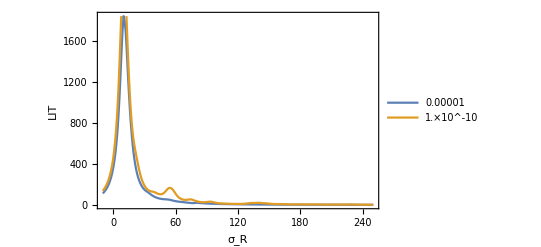

```mathematica
pseudoinverse[threshold_,σR_,σI_]:=Block[{Mm=ham-(σR-σI ⅈ) norm,USA,dimred},PseudoInverse[Mm,Tolerance->threshold]]

thresholds=N[{10^-5,10^-10}];
ListPlot[(Function[{σR},Block[{mm,coeff},mm=pseudoinverse[#,σR,σI];coeff=mm.inhomo;{σR,Chop[Conjugate[coeff].norm.coeff]}]]/@σRs)&/@thresholds,PlotRange->{All,All},Joined->True,Frame->True,FrameLabel->{"σ_R","LIT"},PlotLegends->thresholds]
```

Here we see one of the potential problems of this approach: eigenvalues can slip through the tolerance as we change σ_R, changing the result drastically. That is a real worry!

#### Alternative approach (norm zero-mode removal)

```mathematica
Clear[normreg];normreg[threshold_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];{μs,Or}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]<=threshold&]];{(Transpose[transf].DiagonalMatrix[μ^(-1/2)]),Or,μs}]
```

```mathematica
Clear[decompose];decompose[threshold_,pr_:False,debug_:False]:= Block[{Oμ,Or,μs,oλs,otrf},{Oμ,Or,μs}=normreg[threshold];If[debug,Print[MatrixForm[Chop[(Transpose[Oμ].norm).Oμ]]]];{λs,trf}=Eigensystem[(Transpose[Oμ].ham).Oμ];If[pr,Print["overlap of ψ with norm zero modes (norm, overlap)\n",MatrixForm[Transpose[{μs,Or.inhomo}]]]];{λs,trf.(Transpose[Oμ].inhomo)}]
```

```mathematica
litcomp[threshold_]:=Block[{λscf=Transpose[decompose[threshold]]},Plus@@(((#[[2]])^2/((#[[1]]-σRe)^2+σIm^2))&/@λscf)]
litshow[threshold_]:=Block[{λscf=Transpose[decompose[threshold]]},{#[[1]],Abs[#[[2]]]^2}&/@λscf]
```

This exposes a problem, the r.h.s has non-zero components (or at least components much larger than √μ) in the direction of the zero modes. This means solution of the inversion problem is very unstable under change of the number of components, as we shall see below.

```mathematica
decompose[10^-8,True,False]
```

overlap of ψ with norm zero modes (norm, overlap)
(-1.55575×10^-14 | 0.0000371956
1.11073×10^-14 | 0.0000393358
1.86839×10^-14 | 0.0000118897
3.6535×10^-14 | -0.0000715757
4.09142×10^-14 | -0.000192901
4.80676×10^-14 | 0.000149054
6.7996×10^-14 | -0.0000163698
9.43501×10^-14 | 0.000200359
9.7974×10^-14 | -6.62722×10^-7
1.03011×10^-13 | -0.000380601
1.04161×10^-13 | 0.0000184112
1.35615×10^-13 | 0.000156796
1.3624×10^-13 | -0.000890046
1.62286×10^-13 | 0.00186819
1.8794×10^-13 | 0.000197806
2.35708×10^-13 | -0.0000414601
2.38958×10^-13 | 0.000618791
2.75344×10^-13 | -0.000328172
2.9876×10^-13 | 0.000103103
3.23026×10^-13 | -0.000755427
3.41455×10^-13 | 0.000392776
3.76568×10^-13 | -0.000164967
4.19156×10^-13 | -0.000633494
4.40683×10^-13 | 0.000473396
4.73381×10^-13 | 0.000542959
5.3544×10^-13 | -0.000142275
5.84414×10^-13 | -0.0000518521
5.96881×10^-13 | 0.00177529
6.40483×10^-13 | 0.000254381
6.83757×10^-13 | 0.00122181
6.96056×10^-13 | 0.00172289
7.7159×10^-13 | 0.00270067
7.75702×10^-13 | -0.000720477
8.71236×10^-13 | -0.000153612
9.92775×10^-13 | 0.00104839
1.11724×10^-12 | 0.000566339
1.14778×10^-12 | 0.000383352
1.19547×10^-12 | 0.00267089
1.29885×10^-12 | -0.00004712
1.34308×10^-12 | 0.0000257052
1.50045×10^-12 | 0.000604065
1.70394×10^-12 | 0.000337924
1.79315×10^-12 | -0.0000904533
1.84322×10^-12 | -0.000233491
1.98879×10^-12 | -0.000946198
2.02626×10^-12 | 0.00192112
2.13398×10^-12 | -0.00125086
2.25293×10^-12 | 0.0000624943
2.39535×10^-12 | -0.000749396
2.50389×10^-12 | 0.002033
2.56062×10^-12 | 0.00105694
2.60443×10^-12 | 0.000571675
2.79099×10^-12 | -0.0000631475
2.96356×10^-12 | 0.000205505
3.0615×10^-12 | -0.000778194
3.4024×10^-12 | 0.00491589
3.43218×10^-12 | -0.00129369
3.46339×10^-12 | 0.00473176
3.67848×10^-12 | -0.000245689
3.75516×10^-12 | 0.00421922
4.89356×10^-12 | -0.00119496
4.96834×10^-12 | -0.000365421
5.39154×10^-12 | 0.00157856
5.53255×10^-12 | -0.001092
5.89219×10^-12 | 0.0132018
6.06139×10^-12 | 0.00408923
6.42049×10^-12 | -0.0000528318
6.49055×10^-12 | -0.000665929
6.67444×10^-12 | -0.00360537
6.84675×10^-12 | -0.00130054
7.21504×10^-12 | -0.0010058
7.97029×10^-12 | 0.00311002
8.29337×10^-12 | -0.000928904
8.44548×10^-12 | 0.0011574
8.84463×10^-12 | -0.00108518
9.40611×10^-12 | -0.00086196
9.64461×10^-12 | 0.0010575
1.03418×10^-11 | -0.000808062
1.03692×10^-11 | 0.0152881
1.09516×10^-11 | -0.00087637
1.1019×10^-11 | 0.00150312
1.17685×10^-11 | -0.00238429
1.21051×10^-11 | -0.00247524
1.29969×10^-11 | -0.00222302
1.38515×10^-11 | -0.0058063
1.52411×10^-11 | 0.00130895
1.56616×10^-11 | -0.001964
1.63592×10^-11 | 0.00819942
1.80365×10^-11 | -0.00226189
1.80463×10^-11 | -0.0077977
1.90906×10^-11 | -0.00837067
1.98054×10^-11 | 0.00140809
2.19561×10^-11 | -0.000697117
2.20781×10^-11 | -0.00229747
2.21391×10^-11 | -0.001587
2.43623×10^-11 | -0.000591354
2.57999×10^-11 | -0.000663612
2.78317×10^-11 | 0.000745919
2.89446×10^-11 | 0.00964015
2.90397×10^-11 | -0.00214452
2.9673×10^-11 | -0.000775692
2.99864×10^-11 | -0.00230198
3.48367×10^-11 | 0.00159661
3.90748×10^-11 | -0.000310441
3.91087×10^-11 | -0.011111
4.00886×10^-11 | -0.00309986
4.14998×10^-11 | -0.00429183
4.56948×10^-11 | -0.00774332
4.57251×10^-11 | 0.000779973
4.85849×10^-11 | 0.00203383
5.22605×10^-11 | 0.0136051
5.24821×10^-11 | 0.00353298
5.73367×10^-11 | 0.0042589
6.0709×10^-11 | 0.00513243
6.53322×10^-11 | 0.00343623
6.79875×10^-11 | 0.00649913
7.01507×10^-11 | 0.00275499
7.0949×10^-11 | -0.0100001
7.6075×10^-11 | -0.00166923
7.95143×10^-11 | -0.0052402
8.08796×10^-11 | 0.0107103
8.23704×10^-11 | 0.00119606
8.45332×10^-11 | -0.00643476
8.89733×10^-11 | 0.00198877
9.33624×10^-11 | -0.00129437
9.67611×10^-11 | -0.0058576
9.69237×10^-11 | 0.0201139
1.0568×10^-10 | -0.00450698
1.06861×10^-10 | 0.00507759
1.09267×10^-10 | 0.0264021
1.11945×10^-10 | -0.00325115
1.15383×10^-10 | -0.00130742
1.21658×10^-10 | 0.00530558
1.32685×10^-10 | 0.00921908
1.34492×10^-10 | 0.00282347
1.39941×10^-10 | 0.00360438
1.42099×10^-10 | -0.00292301
1.43922×10^-10 | -0.00791943
1.52531×10^-10 | -0.0230566
1.6503×10^-10 | 0.00879263
1.65106×10^-10 | 0.0143412
1.73101×10^-10 | 0.00789886
1.78007×10^-10 | 0.0402509
1.83342×10^-10 | -0.00946323
1.85569×10^-10 | -0.0256104
1.99234×10^-10 | 0.000121781
2.0036×10^-10 | 0.0199471
2.04619×10^-10 | 0.005476
2.14614×10^-10 | -0.00443888
2.22877×10^-10 | -0.00318351
2.27081×10^-10 | 0.027842
2.35394×10^-10 | -0.00257525
2.43439×10^-10 | -0.129926
2.59501×10^-10 | -0.011899
2.77108×10^-10 | -0.0112912
2.87703×10^-10 | 0.00522234
2.90634×10^-10 | 0.0270117
2.97294×10^-10 | 0.00897706
3.12598×10^-10 | 0.063192
3.13114×10^-10 | 0.000813744
3.38721×10^-10 | -0.00146123
3.46388×10^-10 | -0.0122986
3.79827×10^-10 | -0.000462019
3.81467×10^-10 | -0.0185249
3.97298×10^-10 | -0.00535031
4.00501×10^-10 | 0.0378462
4.06694×10^-10 | 0.00160975
4.17677×10^-10 | -0.00829797
4.40358×10^-10 | -0.00261027
4.52064×10^-10 | -0.000303459
4.75071×10^-10 | 0.00268867
4.8838×10^-10 | 0.00200385
4.94842×10^-10 | -0.00823673
5.09656×10^-10 | 0.0285023
5.38128×10^-10 | -0.0331411
5.49433×10^-10 | -0.00572558
5.56497×10^-10 | 0.0358304
5.62974×10^-10 | -0.0407659
5.89501×10^-10 | -0.000225043
6.23926×10^-10 | -0.00526935
6.60483×10^-10 | 0.00445934
7.35985×10^-10 | 0.00358163
7.64422×10^-10 | 0.100323
7.88176×10^-10 | 0.00848255
8.00869×10^-10 | 0.00291148
8.11496×10^-10 | 0.00149075
8.71916×10^-10 | 0.0160092
8.72207×10^-10 | 0.00888538
9.525×10^-10 | -0.00287278
1.01602×10^-9 | 0.0771295
1.04108×10^-9 | 0.0259621
1.05693×10^-9 | -0.0203623
1.07656×10^-9 | -0.0157711
1.19111×10^-9 | 0.00707009
1.21554×10^-9 | -0.0121115
1.2697×10^-9 | 0.00649273
1.36689×10^-9 | 0.00349809
1.39985×10^-9 | 0.0136693
1.45457×10^-9 | 0.0111415
1.45956×10^-9 | -0.000773652
1.49409×10^-9 | 0.000185869
1.53203×10^-9 | 0.00335082
1.58478×10^-9 | 0.00635649
1.69149×10^-9 | -0.0414908
1.73558×10^-9 | 0.000557018
1.74157×10^-9 | -0.0107032
1.79179×10^-9 | -0.000363301
1.81584×10^-9 | 0.00321346
1.83904×10^-9 | 0.00586174
1.98832×10^-9 | -0.121568
2.01258×10^-9 | -0.0252481
2.12718×10^-9 | -0.0267574
2.20984×10^-9 | 0.0818382
2.33812×10^-9 | -0.0335625
2.38934×10^-9 | -0.117052
2.43707×10^-9 | 0.0107212
2.51092×10^-9 | 0.00274986
2.69346×10^-9 | 0.0302531
2.71759×10^-9 | 0.0396112
2.77302×10^-9 | 0.0107953
2.95528×10^-9 | 0.00215934
2.97641×10^-9 | -0.0406354
3.03787×10^-9 | 0.0899305
3.13178×10^-9 | -0.000518205
3.35424×10^-9 | -0.0844071
3.54042×10^-9 | -0.168349
3.54419×10^-9 | -0.0395373
3.58587×10^-9 | 0.00672085
3.65706×10^-9 | -0.00608192
3.84072×10^-9 | 0.00360222
4.08857×10^-9 | -0.0373489
4.26067×10^-9 | -0.0212391
4.38893×10^-9 | -0.173004
4.46766×10^-9 | 0.00221042
4.5396×10^-9 | -0.430642
4.59016×10^-9 | -0.00979142
4.89369×10^-9 | 0.206484
4.96716×10^-9 | 0.0511276
5.03734×10^-9 | 0.0329895
5.22365×10^-9 | -0.00890575
5.50066×10^-9 | -0.0327894
5.69093×10^-9 | 0.062692
5.9637×10^-9 | 0.0126654
6.15447×10^-9 | -0.0222875
6.36303×10^-9 | 0.00761668
6.48144×10^-9 | 0.0710289
6.51888×10^-9 | 0.0572486
6.84751×10^-9 | 0.0290723
6.95456×10^-9 | -0.023394
7.08902×10^-9 | -0.0457677
7.24931×10^-9 | 0.0264287
7.47566×10^-9 | -0.0760526
7.59998×10^-9 | 0.125804
7.83976×10^-9 | 0.0539054
8.28497×10^-9 | 0.0527833
8.59594×10^-9 | 0.0928792
8.77267×10^-9 | -0.0117909
8.98023×10^-9 | 0.0144199
9.54311×10^-9 | 0.0376187
9.60496×10^-9 | -0.118143
9.8965×10^-9 | 0.0301345)

{{-43850.6+0. ⅈ,5368.19+0. ⅈ,5206.86+0. ⅈ,5186.18+0. ⅈ,4921.07+0. ⅈ,4907.18+0. ⅈ,4794.85+0. ⅈ,4764.27+0. ⅈ,4721.64+0. ⅈ,4635.82+0. ⅈ,4576.62+0. ⅈ,4553.94+0. ⅈ,4541.66+0. ⅈ,4507.35+0. ⅈ,4458.41+0. ⅈ,4425.09+0. ⅈ,4397.73+0. ⅈ,4366.94+0. ⅈ,4347.17+0. ⅈ,4319.65+0. ⅈ,4307.39+0. ⅈ,4297.84+0. ⅈ,4252.55+0. ⅈ,4153.43+0. ⅈ,4141.32+0. ⅈ,4133.44+0. ⅈ,4085.79+0. ⅈ,4072.07+0. ⅈ,4040.51+0. ⅈ,4001.52+0. ⅈ,3979.3+0. ⅈ,3963.61+0. ⅈ,3940.01+0. ⅈ,3925.18+0. ⅈ,3891.17+0. ⅈ,3878.76+0. ⅈ,3859.89+0. ⅈ,3790.17+0. ⅈ,3773.26+0. ⅈ,3756.76+0. ⅈ,3747.+0. ⅈ,3700.88+0. ⅈ,3690.79+0. ⅈ,3645.04+0. ⅈ,3616.57+0. ⅈ,3574.89+0. ⅈ,3561.11+0. ⅈ,3542.56+0. ⅈ,3479.71+0. ⅈ,3473.54+0. ⅈ,3470.67+0. ⅈ,3455.78+0. ⅈ,3437.45+0. ⅈ,3392.02+0. ⅈ,3344.29+0. ⅈ,3335.06+0. ⅈ,3324.56+0. ⅈ,3292.59+0. ⅈ,3284.82+0. ⅈ,3277.52+0. ⅈ,3256.32+0. ⅈ,3225.97+0. ⅈ,3183.42+0. ⅈ,3178.17+0. ⅈ,3138.9+0. ⅈ,3100.53+0. ⅈ,3091.78+0. ⅈ,3089.59+0. ⅈ,3084.76+0. ⅈ,3068.59+0. ⅈ,3043.38+0. ⅈ,3031.24+0. ⅈ,3016.84+0. ⅈ,2990.66+0. ⅈ,2969.15+0. ⅈ,2958.04+0. ⅈ,2933.82+0. ⅈ,2915.11+0. ⅈ,2894.94+0. ⅈ,2873.68+0. ⅈ,2864.89+0. ⅈ,2848.77+0. ⅈ,2841.55+0. ⅈ,2833.3+0. ⅈ,2803.77+0. ⅈ,2789.11+0. ⅈ,2772.82+0. ⅈ,2768.86+0. ⅈ,2721.02+0. ⅈ,2710.5+0. ⅈ,2699.69+0. ⅈ,2695.77+0. ⅈ,2690.23+0. ⅈ,2660.36+0. ⅈ,2626.8+0. ⅈ,2617.69+0. ⅈ,2600.21+0. ⅈ,2589.45+0. ⅈ,2569.76+0. ⅈ,2561.2+0. ⅈ,2556.21+0. ⅈ,2546.97+6.22486 ⅈ,2546.97-6.22486 ⅈ,2539.04+0. ⅈ,2494.97+0. ⅈ,2490.3+0. ⅈ,2482.36+0. ⅈ,2477.27+0. ⅈ,2460.9+0. ⅈ,2455.06+0. ⅈ,2445.1+0. ⅈ,2435.55+0. ⅈ,2433.55+0. ⅈ,2415.44+0. ⅈ,2409.85+0. ⅈ,2386.99+0. ⅈ,2362.49+0. ⅈ,2346.8+0. ⅈ,2345.39+34.7178 ⅈ,2345.39-34.7178 ⅈ,2329.01+0. ⅈ,2315.96+0. ⅈ,2293.47+0. ⅈ,2265.31+0. ⅈ,2257.51+0. ⅈ,2253.21+0. ⅈ,2234.83+0. ⅈ,2228.8+0. ⅈ,2218.93+0. ⅈ,2194.86+0. ⅈ,2190.35+0. ⅈ,2188.75+0. ⅈ,2174.63+0. ⅈ,2159.23+0. ⅈ,2152.99+0. ⅈ,2147.15+0. ⅈ,2132.25+0. ⅈ,2124.51+0. ⅈ,2099.9+0. ⅈ,2094.19+0. ⅈ,2080.09+0. ⅈ,2070.28+0. ⅈ,2059.41+0. ⅈ,2050.96+0. ⅈ,2041.85+0. ⅈ,2037.22+0. ⅈ,2029.55+0. ⅈ,2010.62+0. ⅈ,1975.15+0. ⅈ,1974.37+0. ⅈ,1956.69+0. ⅈ,1953.72+0. ⅈ,1934.33+0. ⅈ,1925.52+0. ⅈ,1919.94+0. ⅈ,1901.92+0. ⅈ,1882.99+0. ⅈ,1865.27+0. ⅈ,1856.61+0. ⅈ,1850.25+0. ⅈ,1839.89+0. ⅈ,1824.91+0. ⅈ,1813.82+0. ⅈ,1812.5+0. ⅈ,1803.5+0. ⅈ,1801.79+0. ⅈ,1785.04+0. ⅈ,1773.83+0. ⅈ,1771.66+0. ⅈ,1767.27+0. ⅈ,1764.54+0. ⅈ,1746.74+0. ⅈ,1737.99+28.8408 ⅈ,1737.99-28.8408 ⅈ,1737.92+0. ⅈ,1729.38+0. ⅈ,1719.47+0. ⅈ,1711.61+0. ⅈ,1690.42+2.867 ⅈ,1690.42-2.867 ⅈ,1680.37+0. ⅈ,1665.35+0. ⅈ,1660.43+0. ⅈ,1653.84+9.35778 ⅈ,1653.84-9.35778 ⅈ,1637.38+0. ⅈ,1637.22+14.7464 ⅈ,1637.22-14.7464 ⅈ,1618.88+0. ⅈ,1607.35+3.34005 ⅈ,1607.35-3.34005 ⅈ,1604.75+0. ⅈ,1595.44+0. ⅈ,1584.37+0. ⅈ,1577.8+0. ⅈ,1574.38+0. ⅈ,1557.73+0. ⅈ,1553.83+0. ⅈ,1548.44+0.430758 ⅈ,1548.44-0.430758 ⅈ,1536.03+0. ⅈ,1534.08+0. ⅈ,1519.82+0. ⅈ,1509.23+0. ⅈ,1489.87+0. ⅈ,1482.82+0. ⅈ,1475.19+0. ⅈ,1466.6+0. ⅈ,1457.71+0. ⅈ,1437.26+0. ⅈ,1426.24+0. ⅈ,1422.44+0. ⅈ,1420.2+0. ⅈ,1412.3+0. ⅈ,1408.91+0. ⅈ,1404.39+0. ⅈ,1392.16+0. ⅈ,1385.97+0. ⅈ,1382.6+0. ⅈ,1372.99+0. ⅈ,1360.59+0. ⅈ,1358.18+0. ⅈ,1354.81+0. ⅈ,-1351.91+0. ⅈ,1346.39+0. ⅈ,1343.09+0. ⅈ,1339.64+0. ⅈ,1334.95+0. ⅈ,1332.32+0. ⅈ,1330.27+0. ⅈ,1321.44+0. ⅈ,1317.39+0. ⅈ,1308.42+0. ⅈ,1296.51+0. ⅈ,1289.6+0. ⅈ,1284.32+1.71052 ⅈ,1284.32-1.71052 ⅈ,1280.74+0. ⅈ,1257.55+0. ⅈ,1249.19+2.35235 ⅈ,1249.19-2.35235 ⅈ,1244.23+0. ⅈ,1238.53+0. ⅈ,1234.53+0. ⅈ,1225.41+0. ⅈ,1224.55+0. ⅈ,1207.62+0. ⅈ,1197.68+0. ⅈ,1184.19+0. ⅈ,1178.51+7.49895 ⅈ,1178.51-7.49895 ⅈ,1172.64+0. ⅈ,1171.01+0. ⅈ,1151.55+0.396595 ⅈ,1151.55-0.396595 ⅈ,1138.2+0. ⅈ,1129.39+0. ⅈ,1127.49+0. ⅈ,1117.24+10.8762 ⅈ,1117.24-10.8762 ⅈ,1113.61+0. ⅈ,1108.72+0. ⅈ,1095.27+0. ⅈ,1088.19+0. ⅈ,1084.33+5.10844 ⅈ,1084.33-5.10844 ⅈ,1081.44+0. ⅈ,1072.65+3.43828 ⅈ,1072.65-3.43828 ⅈ,1068.42+0. ⅈ,1065.03+0. ⅈ,1057.27+0. ⅈ,1053.32+0. ⅈ,1047.83+4.71055 ⅈ,1047.83-4.71055 ⅈ,1046.24+0. ⅈ,1042.94+0. ⅈ,1036.68+2.16176 ⅈ,1036.68-2.16176 ⅈ,1032.01+0. ⅈ,1022.83+0. ⅈ,1022.56+0. ⅈ,1016.32+4.60698 ⅈ,1016.32-4.60698 ⅈ,1005.85+1.13306 ⅈ,1005.85-1.13306 ⅈ,1001.56+0. ⅈ,997.303+0. ⅈ,990.171+0. ⅈ,984.555+0. ⅈ,978.496+0. ⅈ,976.621+0. ⅈ,974.158+0. ⅈ,969.461+0. ⅈ,966.169+0. ⅈ,964.742+0. ⅈ,958.01+0. ⅈ,956.383+0. ⅈ,953.669+0. ⅈ,941.554+0. ⅈ,936.654+0. ⅈ,933.4+0. ⅈ,926.446+0.0934636 ⅈ,926.446-0.0934636 ⅈ,916.884+0. ⅈ,910.794+0. ⅈ,906.116+0. ⅈ,900.604+0. ⅈ,899.119+0. ⅈ,890.364+0. ⅈ,884.926+0. ⅈ,882.391+0. ⅈ,873.982+0. ⅈ,870.913+0. ⅈ,865.715+0. ⅈ,864.45+0. ⅈ,856.875+0. ⅈ,854.48+0. ⅈ,848.681+0. ⅈ,841.592+0. ⅈ,836.591+0. ⅈ,834.163+0. ⅈ,830.404+0. ⅈ,824.402+0. ⅈ,817.134+0.254875 ⅈ,817.134-0.254875 ⅈ,809.983+0. ⅈ,806.05+0. ⅈ,803.028+0. ⅈ,796.64+5.39148 ⅈ,796.64-5.39148 ⅈ,796.338+0. ⅈ,789.002+0. ⅈ,788.829+0. ⅈ,784.297+0. ⅈ,771.208+0. ⅈ,763.594+0. ⅈ,763.2+0. ⅈ,760.967+0. ⅈ,758.353+0. ⅈ,754.823+0. ⅈ,752.525+0. ⅈ,747.784+0. ⅈ,745.959+0. ⅈ,740.471+0. ⅈ,738.485+0. ⅈ,726.895+2.27812 ⅈ,726.895-2.27812 ⅈ,723.949+1.49195 ⅈ,723.949-1.49195 ⅈ,721.794+0. ⅈ,719.397+13.9156 ⅈ,719.397-13.9156 ⅈ,709.332+2.03725 ⅈ,709.332-2.03725 ⅈ,707.84+0. ⅈ,703.806+0. ⅈ,699.24+0. ⅈ,697.46+0. ⅈ,688.549+0. ⅈ,687.155+0. ⅈ,685.192+0. ⅈ,679.956+2.52355 ⅈ,679.956-2.52355 ⅈ,671.229+0. ⅈ,667.846+0.826668 ⅈ,667.846-0.826668 ⅈ,662.625+0. ⅈ,659.941+0.131641 ⅈ,659.941-0.131641 ⅈ,652.462+0. ⅈ,650.34+0. ⅈ,645.169+0. ⅈ,644.026+4.16726 ⅈ,644.026-4.16726 ⅈ,638.075+0. ⅈ,636.071+0. ⅈ,632.04+0. ⅈ,627.718+0. ⅈ,624.456+0. ⅈ,622.26+0. ⅈ,618.997+0. ⅈ,614.368+0. ⅈ,608.457+0. ⅈ,605.402+9.00052 ⅈ,605.402-9.00052 ⅈ,601.998+0. ⅈ,601.562+0. ⅈ,596.377+0. ⅈ,594.267+0. ⅈ,588.346+8.2487 ⅈ,588.346-8.2487 ⅈ,587.089+0. ⅈ,584.519+0. ⅈ,579.165+0. ⅈ,577.481+6.57564 ⅈ,577.481-6.57564 ⅈ,568.782+0. ⅈ,565.285+3.65159 ⅈ,565.285-3.65159 ⅈ,562.713+2.54429 ⅈ,562.713-2.54429 ⅈ,557.292+0. ⅈ,553.304+0. ⅈ,550.817+0. ⅈ,547.339+0. ⅈ,545.723+0. ⅈ,544.366+0. ⅈ,539.439+0. ⅈ,538.259+0. ⅈ,537.167+0. ⅈ,535.295+0. ⅈ,533.803+0. ⅈ,529.076+0. ⅈ,525.794+0. ⅈ,522.504+0. ⅈ,519.13+0. ⅈ,516.657+1.95725 ⅈ,516.657-1.95725 ⅈ,512.08+0. ⅈ,510.261+0. ⅈ,506.206+0. ⅈ,505.405+1.01255 ⅈ,505.405-1.01255 ⅈ,500.734+0. ⅈ,497.991+0. ⅈ,493.228+0. ⅈ,489.896+4.6763 ⅈ,489.896-4.6763 ⅈ,487.357+0. ⅈ,481.928+0. ⅈ,478.669+1.47088 ⅈ,478.669-1.47088 ⅈ,476.479+0. ⅈ,474.79+0. ⅈ,472.173+0. ⅈ,469.133+3.16385 ⅈ,469.133-3.16385 ⅈ,463.875+0. ⅈ,461.368+0. ⅈ,460.973+0. ⅈ,457.291+4.1317 ⅈ,457.291-4.1317 ⅈ,456.941+0. ⅈ,452.155+1.60132 ⅈ,452.155-1.60132 ⅈ,448.758+0. ⅈ,443.771+0. ⅈ,442.551+0. ⅈ,440.609+0. ⅈ,435.421+0. ⅈ,434.423+0.988358 ⅈ,434.423-0.988358 ⅈ,432.071+1.63695 ⅈ,432.071-1.63695 ⅈ,428.131+0. ⅈ,425.091+0. ⅈ,422.628+0. ⅈ,421.42+0. ⅈ,416.938+0. ⅈ,413.501+1.06505 ⅈ,413.501-1.06505 ⅈ,408.591+0. ⅈ,406.971+0. ⅈ,405.584+0. ⅈ,402.428+0. ⅈ,401.588+0. ⅈ,399.214+0. ⅈ,397.292+0. ⅈ,394.793+0. ⅈ,392.62+2.77898 ⅈ,392.62-2.77898 ⅈ,391.9+0. ⅈ,383.998+0.901449 ⅈ,383.998-0.901449 ⅈ,381.22+0.79468 ⅈ,381.22-0.79468 ⅈ,381.024+5.93335 ⅈ,381.024-5.93335 ⅈ,373.367+0. ⅈ,373.182+1.37809 ⅈ,373.182-1.37809 ⅈ,370.876+0. ⅈ,368.323+0. ⅈ,366.657+2.46663 ⅈ,366.657-2.46663 ⅈ,363.961+0. ⅈ,360.168+0. ⅈ,358.031+0. ⅈ,356.792+0. ⅈ,355.483+0. ⅈ,351.919+0. ⅈ,347.99+0.638268 ⅈ,347.99-0.638268 ⅈ,346.256+1.02188 ⅈ,346.256-1.02188 ⅈ,343.428+0. ⅈ,341.352+0. ⅈ,338.415+0.114257 ⅈ,338.415-0.114257 ⅈ,334.974+0. ⅈ,331.802+0.0928131 ⅈ,331.802-0.0928131 ⅈ,326.855+0. ⅈ,326.058+1.91254 ⅈ,326.058-1.91254 ⅈ,323.318+0. ⅈ,321.641+1.53904 ⅈ,321.641-1.53904 ⅈ,317.499+0.326607 ⅈ,317.499-0.326607 ⅈ,313.724+0. ⅈ,309.759+0.939214 ⅈ,309.759-0.939214 ⅈ,306.619+0. ⅈ,305.247+0. ⅈ,299.595+2.4975 ⅈ,299.595-2.4975 ⅈ,299.376+0. ⅈ,299.018+0. ⅈ,296.889+0. ⅈ,294.135+0. ⅈ,292.264+0. ⅈ,288.585+0. ⅈ,285.77+0. ⅈ,284.627+0. ⅈ,283.765+0. ⅈ,282.521+0. ⅈ,281.076+0. ⅈ,278.753+0. ⅈ,277.223+0. ⅈ,274.789+0. ⅈ,272.784+0. ⅈ,271.01+0. ⅈ,269.08+0.524767 ⅈ,269.08-0.524767 ⅈ,267.394+0. ⅈ,265.839+0. ⅈ,263.51+1.18401 ⅈ,263.51-1.18401 ⅈ,262.592+0. ⅈ,259.805+2.1553 ⅈ,259.805-2.1553 ⅈ,258.017+0. ⅈ,255.156+0. ⅈ,253.216+11.0337 ⅈ,253.216-11.0337 ⅈ,253.025+0.372958 ⅈ,253.025-0.372958 ⅈ,251.064+0. ⅈ,249.397+0. ⅈ,247.091+0. ⅈ,246.309+0. ⅈ,244.085+0. ⅈ,242.279+0.284317 ⅈ,242.279-0.284317 ⅈ,239.5+0. ⅈ,238.927+0. ⅈ,238.045+0. ⅈ,236.624+0. ⅈ,235.918+0. ⅈ,233.057+0. ⅈ,231.448+1.34942 ⅈ,231.448-1.34942 ⅈ,230.619+0. ⅈ,229.922+0. ⅈ,225.08+0. ⅈ,225.052+2.841 ⅈ,225.052-2.841 ⅈ,222.706+1.06863 ⅈ,222.706-1.06863 ⅈ,220.081+0. ⅈ,218.962+0. ⅈ,217.573+0. ⅈ,215.758+0.153779 ⅈ,215.758-0.153779 ⅈ,214.016+0. ⅈ,212.047+0. ⅈ,210.509+0. ⅈ,208.125+1.1358 ⅈ,208.125-1.1358 ⅈ,205.949+0.438446 ⅈ,205.949-0.438446 ⅈ,203.231+0. ⅈ,202.495+0. ⅈ,200.923+0.159202 ⅈ,200.923-0.159202 ⅈ,200.316+0. ⅈ,199.942+0. ⅈ,198.173+0. ⅈ,196.863+0. ⅈ,195.843+0. ⅈ,194.298+0. ⅈ,193.432+0. ⅈ,192.091+0. ⅈ,190.743+0. ⅈ,189.294+0. ⅈ,187.9+0. ⅈ,186.632+0. ⅈ,185.125+0. ⅈ,183.03+0. ⅈ,180.977+0. ⅈ,179.734+0. ⅈ,-155.987+87.7806 ⅈ,-155.987-87.7806 ⅈ,178.953+0.415144 ⅈ,178.953-0.415144 ⅈ,177.868+0. ⅈ,176.576+0. ⅈ,175.095+0. ⅈ,174.669+0. ⅈ,174.399+0. ⅈ,172.679+0. ⅈ,171.48+0. ⅈ,169.491+0. ⅈ,168.065+0. ⅈ,167.431+0. ⅈ,164.669+0. ⅈ,163.164+0.0815935 ⅈ,163.164-0.0815935 ⅈ,160.933+0. ⅈ,160.37+0. ⅈ,159.062+0. ⅈ,158.583+0. ⅈ,157.486+0.271714 ⅈ,157.486-0.271714 ⅈ,155.786+0. ⅈ,154.964+0. ⅈ,153.084+0. ⅈ,152.857+0. ⅈ,150.292+4.89858 ⅈ,150.292-4.89858 ⅈ,149.735+0. ⅈ,148.925+0. ⅈ,148.524+0. ⅈ,147.17+0. ⅈ,145.891+0. ⅈ,145.217+0. ⅈ,144.304+0. ⅈ,143.847+0. ⅈ,143.632+0. ⅈ,141.332+0. ⅈ,140.37+0. ⅈ,139.71+0. ⅈ,137.187+0. ⅈ,136.334+0. ⅈ,134.871+0. ⅈ,134.397+0. ⅈ,134.072+0. ⅈ,133.743+0. ⅈ,131.246+0. ⅈ,130.542+0. ⅈ,129.23+0. ⅈ,127.171+0. ⅈ,126.631+0. ⅈ,-126.318+0. ⅈ,124.862+0.625253 ⅈ,124.862-0.625253 ⅈ,123.146+0. ⅈ,121.423+0. ⅈ,121.111+1.21947 ⅈ,121.111-1.21947 ⅈ,120.938+0. ⅈ,119.954+0. ⅈ,118.483+0. ⅈ,117.708+0. ⅈ,116.397+0. ⅈ,115.943+0.7666 ⅈ,115.943-0.7666 ⅈ,114.667+0. ⅈ,112.717+0. ⅈ,112.529+0. ⅈ,110.404+0. ⅈ,109.12+0. ⅈ,108.133+0. ⅈ,107.108+0. ⅈ,106.287+0. ⅈ,105.615+0. ⅈ,104.902+0. ⅈ,103.098+0. ⅈ,102.41+0. ⅈ,101.714+0.427871 ⅈ,101.714-0.427871 ⅈ,99.828+0. ⅈ,98.8663+0. ⅈ,97.1026+0. ⅈ,96.5837+0. ⅈ,96.2393+0. ⅈ,94.6815+0. ⅈ,94.2759+0. ⅈ,93.5419+0. ⅈ,92.097+0. ⅈ,92.0074+0. ⅈ,89.8779+0. ⅈ,89.5198+0. ⅈ,88.2656+0. ⅈ,87.7317+0. ⅈ,87.0329+0. ⅈ,86.245+0. ⅈ,84.441+0. ⅈ,83.1653+0.215915 ⅈ,83.1653-0.215915 ⅈ,81.9381+0. ⅈ,80.3575+0.197092 ⅈ,80.3575-0.197092 ⅈ,79.2483+0. ⅈ,78.008+0.168321 ⅈ,78.008-0.168321 ⅈ,77.3119+0. ⅈ,77.1487+0. ⅈ,76.3087+0. ⅈ,75.9838+0. ⅈ,75.4972+0. ⅈ,73.1793+0. ⅈ,72.6837+0. ⅈ,72.3164+0. ⅈ,71.4887+0. ⅈ,69.7741+0. ⅈ,68.6269+0. ⅈ,68.1087+0. ⅈ,67.394+0. ⅈ,67.0754+0. ⅈ,65.8764+0. ⅈ,63.0962+0. ⅈ,62.6051+0.112157 ⅈ,62.6051-0.112157 ⅈ,61.5772+0. ⅈ,60.132+0. ⅈ,59.9264+0. ⅈ,58.5025+0.647542 ⅈ,58.5025-0.647542 ⅈ,58.2896+0. ⅈ,57.4776+0. ⅈ,57.1685+0. ⅈ,55.4473+0. ⅈ,55.0208+0. ⅈ,54.7009+0. ⅈ,53.9898+0. ⅈ,52.6281+0. ⅈ,51.0164+0. ⅈ,49.0223+0. ⅈ,48.1494+0. ⅈ,47.5206+0. ⅈ,46.5834+0. ⅈ,46.4226+0. ⅈ,45.4858+0. ⅈ,43.8119+0. ⅈ,43.1651+0. ⅈ,41.8989+0. ⅈ,41.6289+0. ⅈ,40.1187+0. ⅈ,39.4063+0. ⅈ,39.079+0. ⅈ,37.7292+0. ⅈ,37.1245+0. ⅈ,36.4563+0. ⅈ,36.2156+0. ⅈ,35.629+0. ⅈ,35.2406+0. ⅈ,32.855+0. ⅈ,32.2648+0. ⅈ,31.8743+0. ⅈ,31.2334+0. ⅈ,30.7339+0. ⅈ,28.9365+0. ⅈ,27.9753+0. ⅈ,27.6356+0. ⅈ,26.1977+0.100367 ⅈ,26.1977-0.100367 ⅈ,24.9504+0. ⅈ,24.2291+0. ⅈ,23.3579+0. ⅈ,21.875+0. ⅈ,21.4714+0. ⅈ,20.7918+0. ⅈ,19.7915+0. ⅈ,19.4391+0. ⅈ,18.4453+0. ⅈ,18.2434+0. ⅈ,17.2173+0. ⅈ,16.7961+0. ⅈ,15.5467+0. ⅈ,14.4917+0. ⅈ,13.603+0. ⅈ,13.1994+0. ⅈ,11.3734+0. ⅈ,10.366+0. ⅈ,9.87997+0. ⅈ,8.05765+0. ⅈ,-6.05371+0. ⅈ,5.9765+0. ⅈ,5.74368+0. ⅈ,3.79791+0. ⅈ,-3.21459+0. ⅈ,1.86464+0. ⅈ},{-5898.39+0. ⅈ,51.816+0. ⅈ,-78.4609+0. ⅈ,-326.105+0. ⅈ,40.4071+0. ⅈ,-107.578+0. ⅈ,-67.53+0. ⅈ,-82.1327+0. ⅈ,-137.124+0. ⅈ,9.49924+0. ⅈ,-133.96+0. ⅈ,144.812+0. ⅈ,-2.96204+0. ⅈ,16.8278+0. ⅈ,77.7452+0. ⅈ,109.582+0. ⅈ,55.2445+0. ⅈ,120.994+0. ⅈ,69.9354+0. ⅈ,-63.7952+0. ⅈ,-37.5085+0. ⅈ,-77.4389+0. ⅈ,380.165+0. ⅈ,-111.864+0. ⅈ,-274.39+0. ⅈ,6.43158+0. ⅈ,33.7636+0. ⅈ,71.964+0. ⅈ,-73.7214+0. ⅈ,42.4936+0. ⅈ,-222.862+0. ⅈ,155.878+0. ⅈ,137.093+0. ⅈ,-107.814+0. ⅈ,165.452+0. ⅈ,238.116+0. ⅈ,-90.8784+0. ⅈ,-103.142+0. ⅈ,41.4641+0. ⅈ,-9.64374+0. ⅈ,-9.69856+0. ⅈ,-100.749+0. ⅈ,-194.924+0. ⅈ,247.177+0. ⅈ,-77.1522+0. ⅈ,-20.1965+0. ⅈ,-4.49847+0. ⅈ,110.807+0. ⅈ,17.4177+0. ⅈ,202.055+0. ⅈ,-76.7754+0. ⅈ,59.7333+0. ⅈ,103.197+0. ⅈ,-133.071+0. ⅈ,-49.8512+0. ⅈ,121.121+0. ⅈ,43.1706+0. ⅈ,80.0218+0. ⅈ,103.866+0. ⅈ,-67.4045+0. ⅈ,143.727+0. ⅈ,24.2416+0. ⅈ,-124.117+0. ⅈ,32.9329+0. ⅈ,306.68+0. ⅈ,-51.2518+0. ⅈ,153.823+0. ⅈ,-98.4476+0. ⅈ,9.71188+0. ⅈ,22.8974+0. ⅈ,-36.8483+0. ⅈ,-245.986+0. ⅈ,-53.3734+0. ⅈ,-122.124+0. ⅈ,161.5+0. ⅈ,57.3552+0. ⅈ,-186.288+0. ⅈ,108.111+0. ⅈ,-116.026+0. ⅈ,-18.3279+0. ⅈ,130.106+0. ⅈ,-31.0406+0. ⅈ,-26.0005+0. ⅈ,-49.1273+0. ⅈ,-46.2134+0. ⅈ,5.17677+0. ⅈ,-368.175+0. ⅈ,114.753+0. ⅈ,-307.211+0. ⅈ,-156.177+0. ⅈ,15.7714+0. ⅈ,-64.2852+0. ⅈ,-281.415+0. ⅈ,-152.623+0. ⅈ,-10.4221+0. ⅈ,72.3602+0. ⅈ,21.9269+0. ⅈ,-40.8529+0. ⅈ,88.3533+0. ⅈ,-171.256+0. ⅈ,168.49+0. ⅈ,-82.9048-66.6412 ⅈ,-82.9048+66.6412 ⅈ,-73.5321+0. ⅈ,1.20685+0. ⅈ,101.777+0. ⅈ,45.1565+0. ⅈ,-3.22738+0. ⅈ,136.124+0. ⅈ,82.8538+0. ⅈ,-25.7323+0. ⅈ,14.5016+0. ⅈ,260.718+0. ⅈ,430.854+0. ⅈ,-200.616+0. ⅈ,-160.297+0. ⅈ,-130.357+0. ⅈ,-40.4069+0. ⅈ,134.775+11.2627 ⅈ,134.775-11.2627 ⅈ,37.7328+0. ⅈ,-5.45307+0. ⅈ,27.7753+0. ⅈ,127.627+0. ⅈ,-301.609+0. ⅈ,78.787+0. ⅈ,110.293+0. ⅈ,-32.5405+0. ⅈ,-102.117+0. ⅈ,6.96648+0. ⅈ,-47.099+0. ⅈ,-167.803+0. ⅈ,-13.1364+0. ⅈ,40.9134+0. ⅈ,7.11603+0. ⅈ,-112.299+0. ⅈ,57.6345+0. ⅈ,-3.24031+0. ⅈ,149.986+0. ⅈ,-150.74+0. ⅈ,-81.1266+0. ⅈ,-372.463+0. ⅈ,-65.545+0. ⅈ,-248.6+0. ⅈ,295.151+0. ⅈ,257.615+0. ⅈ,322.548+0. ⅈ,-181.114+0. ⅈ,25.5223+0. ⅈ,8.64637+0. ⅈ,-36.5789+0. ⅈ,-68.2551+0. ⅈ,42.996+0. ⅈ,173.378+0. ⅈ,-103.506+0. ⅈ,-154.336+0. ⅈ,-106.438+0. ⅈ,49.629+0. ⅈ,-60.0999+0. ⅈ,-117.292+0. ⅈ,120.007+0. ⅈ,-191.379+0. ⅈ,14.8493+0. ⅈ,306.847+0. ⅈ,308.866+0. ⅈ,-1.63641+0. ⅈ,177.225+0. ⅈ,183.283+0. ⅈ,148.824+0. ⅈ,-448.208+0. ⅈ,-111.821+0. ⅈ,206.562+0. ⅈ,129.501-78.2012 ⅈ,129.501+78.2012 ⅈ,-113.445+0. ⅈ,-150.577+0. ⅈ,349.174+0. ⅈ,20.2367+0. ⅈ,54.544-75.9482 ⅈ,54.544+75.9482 ⅈ,-225.273+0. ⅈ,44.5114+0. ⅈ,-267.101+0. ⅈ,148.059-227.617 ⅈ,148.059+227.617 ⅈ,-127.034+0. ⅈ,201.999-117.323 ⅈ,201.999+117.323 ⅈ,67.993+0. ⅈ,-173.576-196.782 ⅈ,-173.576+196.782 ⅈ,-343.396+0. ⅈ,-106.163+0. ⅈ,-157.076+0. ⅈ,52.2107+0. ⅈ,-121.492+0. ⅈ,-139.789+0. ⅈ,171.47+0. ⅈ,2.43998+54.9161 ⅈ,2.43998-54.9161 ⅈ,103.547+0. ⅈ,263.185+0. ⅈ,82.0298+0. ⅈ,14.596+0. ⅈ,74.0593+0. ⅈ,214.678+0. ⅈ,474.385+0. ⅈ,167.037+0. ⅈ,-60.1877+0. ⅈ,-349.752+0. ⅈ,-350.035+0. ⅈ,32.0727+0. ⅈ,54.329+0. ⅈ,-8.99389+0. ⅈ,307.078+0. ⅈ,196.44+0. ⅈ,465.46+0. ⅈ,-286.222+0. ⅈ,-16.795+0. ⅈ,77.3487+0. ⅈ,-151.411+0. ⅈ,-181.955+0. ⅈ,139.514+0. ⅈ,2587.71+0. ⅈ,98.068+0. ⅈ,157.451+0. ⅈ,187.222+0. ⅈ,-108.125+0. ⅈ,-44.0383+0. ⅈ,341.782+0. ⅈ,-281.761+0. ⅈ,-224.416+0. ⅈ,-233.807+0. ⅈ,-164.737+0. ⅈ,104.248+0. ⅈ,9.87451+45.9838 ⅈ,9.87451-45.9838 ⅈ,72.2493+0. ⅈ,-236.156+0. ⅈ,132.31+7.05745 ⅈ,132.31-7.05745 ⅈ,108.391+0. ⅈ,-481.259+0. ⅈ,270.968+0. ⅈ,356.173+0. ⅈ,341.733+0. ⅈ,161.548+0. ⅈ,27.8672+0. ⅈ,434.169+0. ⅈ,301.637+198.084 ⅈ,301.637-198.084 ⅈ,178.091+0. ⅈ,-348.044+0. ⅈ,-90.3192+0.032281 ⅈ,-90.3192-0.032281 ⅈ,159.142+0. ⅈ,240.282+0. ⅈ,151.607+0. ⅈ,-200.308-22.8784 ⅈ,-200.308+22.8784 ⅈ,-56.1795+0. ⅈ,-424.654+0. ⅈ,450.754+0. ⅈ,-224.441+0. ⅈ,-163.779-45.3819 ⅈ,-163.779+45.3819 ⅈ,96.8723+0. ⅈ,75.5621-113.848 ⅈ,75.5621+113.848 ⅈ,236.462+0. ⅈ,47.692+0. ⅈ,186.442+0. ⅈ,141.155+0. ⅈ,77.6015+116.978 ⅈ,77.6015-116.978 ⅈ,-224.616+0. ⅈ,392.593+0. ⅈ,-30.1446-89.6652 ⅈ,-30.1446+89.6652 ⅈ,-7.92425+0. ⅈ,-249.581+0. ⅈ,-248.38+0. ⅈ,-156.698-37.9752 ⅈ,-156.698+37.9752 ⅈ,-88.1955+38.0038 ⅈ,-88.1955-38.0038 ⅈ,-8.93113+0. ⅈ,-71.5662+0. ⅈ,-135.583+0. ⅈ,39.0041+0. ⅈ,-230.086+0. ⅈ,-239.098+0. ⅈ,288.477+0. ⅈ,202.456+0. ⅈ,-156.666+0. ⅈ,234.718+0. ⅈ,-234.32+0. ⅈ,176.42+0. ⅈ,208.663+0. ⅈ,50.3321+0. ⅈ,45.033+0. ⅈ,41.0236+0. ⅈ,-522.368+17.3805 ⅈ,-522.368-17.3805 ⅈ,161.517+0. ⅈ,342.809+0. ⅈ,-139.931+0. ⅈ,123.795+0. ⅈ,-423.826+0. ⅈ,-653.26+0. ⅈ,-100.976+0. ⅈ,585.132+0. ⅈ,-10.8454+0. ⅈ,-43.7129+0. ⅈ,216.234+0. ⅈ,163.13+0. ⅈ,133.082+0. ⅈ,-468.819+0. ⅈ,-150.079+0. ⅈ,-38.9149+0. ⅈ,116.154+0. ⅈ,334.721+0. ⅈ,356.13+0. ⅈ,271.112+0. ⅈ,85.939+13.4194 ⅈ,85.939-13.4194 ⅈ,238.688+0. ⅈ,208.124+0. ⅈ,135.478+0. ⅈ,-66.148-1.80219 ⅈ,-66.148+1.80219 ⅈ,-227.028+0. ⅈ,-60.8015+0. ⅈ,-52.0902+0. ⅈ,-67.5038+0. ⅈ,-304.944+0. ⅈ,101.431+0. ⅈ,-117.652+0. ⅈ,209.038+0. ⅈ,-151.512+0. ⅈ,243.484+0. ⅈ,112.973+0. ⅈ,-65.4168+0. ⅈ,-32.4661+0. ⅈ,-294.204+0. ⅈ,-326.794+0. ⅈ,-68.1936-20.7947 ⅈ,-68.1936+20.7947 ⅈ,5.92874-107.552 ⅈ,5.92874+107.552 ⅈ,202.083+0. ⅈ,259.506-130.171 ⅈ,259.506+130.171 ⅈ,-578.722-180.938 ⅈ,-578.722+180.938 ⅈ,122.23+0. ⅈ,-179.594+0. ⅈ,-150.128+0. ⅈ,-201.676+0. ⅈ,217.796+0. ⅈ,-176.5+0. ⅈ,-182.841+0. ⅈ,-118.524-69.0344 ⅈ,-118.524+69.0344 ⅈ,-9.65404+0. ⅈ,198.283-6.99655 ⅈ,198.283+6.99655 ⅈ,168.657+0. ⅈ,430.673+11.733 ⅈ,430.673-11.733 ⅈ,-815.775+0. ⅈ,-268.821+0. ⅈ,672.226+0. ⅈ,501.019-39.7482 ⅈ,501.019+39.7482 ⅈ,450.748+0. ⅈ,-140.589+0. ⅈ,332.888+0. ⅈ,-285.282+0. ⅈ,61.1163+0. ⅈ,-49.0396+0. ⅈ,208.434+0. ⅈ,-84.846+0. ⅈ,327.17+0. ⅈ,518.72-132.189 ⅈ,518.72+132.189 ⅈ,221.466+0. ⅈ,-348.589+0. ⅈ,-461.535+0. ⅈ,-596.252+0. ⅈ,36.3907+160.732 ⅈ,36.3907-160.732 ⅈ,921.195+0. ⅈ,-881.041+0. ⅈ,511.175+0. ⅈ,219.571+13.4762 ⅈ,219.571-13.4762 ⅈ,322.12+0. ⅈ,89.9317+11.9423 ⅈ,89.9317-11.9423 ⅈ,45.4493-39.3049 ⅈ,45.4493+39.3049 ⅈ,316.123+0. ⅈ,534.513+0. ⅈ,214.179+0. ⅈ,-382.584+0. ⅈ,107.056+0. ⅈ,223.665+0. ⅈ,21.2165+0. ⅈ,10.1181+0. ⅈ,135.732+0. ⅈ,35.7338+0. ⅈ,-320.937+0. ⅈ,82.6306+0. ⅈ,360.803+0. ⅈ,-237.751+0. ⅈ,-38.5585+0. ⅈ,-162.169+63.8183 ⅈ,-162.169-63.8183 ⅈ,-103.068+0. ⅈ,-85.52+0. ⅈ,66.713+0. ⅈ,-183.564+8.48991 ⅈ,-183.564-8.48991 ⅈ,-315.745+0. ⅈ,0.869502+0. ⅈ,-505.5+0. ⅈ,-325.076-44.8341 ⅈ,-325.076+44.8341 ⅈ,-357.019+0. ⅈ,88.6173+0. ⅈ,19.1565+96.8716 ⅈ,19.1565-96.8716 ⅈ,272.412+0. ⅈ,96.5821+0. ⅈ,-41.2767+0. ⅈ,-159.013+315.189 ⅈ,-159.013-315.189 ⅈ,-259.932+0. ⅈ,540.297+0. ⅈ,381.387+0. ⅈ,-218.121-558.83 ⅈ,-218.121+558.83 ⅈ,-366.081+0. ⅈ,83.9276+111.804 ⅈ,83.9276-111.804 ⅈ,-3.72051+0. ⅈ,-248.41+0. ⅈ,-322.531+0. ⅈ,53.7555+0. ⅈ,400.844+0. ⅈ,58.4468-80.6253 ⅈ,58.4468+80.6253 ⅈ,141.187-196.725 ⅈ,141.187+196.725 ⅈ,-233.104+0. ⅈ,-306.631+0. ⅈ,435.129+0. ⅈ,-226.175+0. ⅈ,-70.3167+0. ⅈ,272.498-85.663 ⅈ,272.498+85.663 ⅈ,430.224+0. ⅈ,1068.31+0. ⅈ,-898.306+0. ⅈ,300.182+0. ⅈ,-69.1395+0. ⅈ,-400.607+0. ⅈ,52.2558+0. ⅈ,-303.037+0. ⅈ,-126.552-119.94 ⅈ,-126.552+119.94 ⅈ,126.49+0. ⅈ,-44.1866+29.8279 ⅈ,-44.1866-29.8279 ⅈ,267.741-10.7478 ⅈ,267.741+10.7478 ⅈ,-190.196+243.264 ⅈ,-190.196-243.264 ⅈ,623.731+0. ⅈ,-259.9+327.107 ⅈ,-259.9-327.107 ⅈ,-1140.22+0. ⅈ,592.514+0. ⅈ,86.112-380.566 ⅈ,86.112+380.566 ⅈ,-568.501+0. ⅈ,-385.06+0. ⅈ,-649.417+0. ⅈ,-534.209+0. ⅈ,-201.294+0. ⅈ,-302.379+0. ⅈ,-9.70299-237.843 ⅈ,-9.70299+237.843 ⅈ,121.814+26.3092 ⅈ,121.814-26.3092 ⅈ,285.179+0. ⅈ,487.7+0. ⅈ,-809.434+41.2873 ⅈ,-809.434-41.2873 ⅈ,48.4414+0. ⅈ,-863.832-12.229 ⅈ,-863.832+12.229 ⅈ,166.365+0. ⅈ,-72.1943+26.4791 ⅈ,-72.1943-26.4791 ⅈ,64.3314+0. ⅈ,120.106-204.212 ⅈ,120.106+204.212 ⅈ,269.574+35.4221 ⅈ,269.574-35.4221 ⅈ,142.285+0. ⅈ,100.893-121.205 ⅈ,100.893+121.205 ⅈ,29.2376+0. ⅈ,108.843+0. ⅈ,-198.349-116.491 ⅈ,-198.349+116.491 ⅈ,159.804+0. ⅈ,-216.885+0. ⅈ,-315.171+0. ⅈ,528.871+0. ⅈ,145.081+0. ⅈ,-62.468+0. ⅈ,58.0472+0. ⅈ,-419.694+0. ⅈ,63.4236+0. ⅈ,-559.654+0. ⅈ,124.806+0. ⅈ,317.753+0. ⅈ,-451.191+0. ⅈ,-560.337+0. ⅈ,-342.582+0. ⅈ,139.212+0. ⅈ,95.6451-181.652 ⅈ,95.6451+181.652 ⅈ,-265.46+0. ⅈ,17.9629+0. ⅈ,-202.396+281.994 ⅈ,-202.396-281.994 ⅈ,-210.859+0. ⅈ,46.4404-240.652 ⅈ,46.4404+240.652 ⅈ,-107.693+0. ⅈ,541.756+0. ⅈ,-27.8878-56.9238 ⅈ,-27.8878+56.9238 ⅈ,-89.6566-50.2322 ⅈ,-89.6566+50.2322 ⅈ,-719.846+0. ⅈ,92.2127+0. ⅈ,-499.369+0. ⅈ,-797.954+0. ⅈ,-282.812+0. ⅈ,873.866-175.639 ⅈ,873.866+175.639 ⅈ,633.261+0. ⅈ,-908.174+0. ⅈ,-586.277+0. ⅈ,751.242+0. ⅈ,309.947+0. ⅈ,-239.354+0. ⅈ,-283.418-428.705 ⅈ,-283.418+428.705 ⅈ,-70.6697+0. ⅈ,576.436+0. ⅈ,312.233+0. ⅈ,436.878-101.964 ⅈ,436.878+101.964 ⅈ,-146.158-87.0724 ⅈ,-146.158+87.0724 ⅈ,422.272+0. ⅈ,738.626+0. ⅈ,-142.101+0. ⅈ,-91.823+31.9909 ⅈ,-91.823-31.9909 ⅈ,-1082.98+0. ⅈ,-1457.55+0. ⅈ,-590.148+0. ⅈ,628.491+47.4173 ⅈ,628.491-47.4173 ⅈ,425.008+48.598 ⅈ,425.008-48.598 ⅈ,571.237+0. ⅈ,-252.516+0. ⅈ,-86.7892-89.7439 ⅈ,-86.7892+89.7439 ⅈ,-287.123+0. ⅈ,-20.7349+0. ⅈ,-350.158+0. ⅈ,-519.85+0. ⅈ,-819.664+0. ⅈ,-70.0624+0. ⅈ,-142.584+0. ⅈ,400.637+0. ⅈ,-155.741+0. ⅈ,238.938+0. ⅈ,47.0712+0. ⅈ,-161.671+0. ⅈ,-323.123+0. ⅈ,-455.861+0. ⅈ,895.592+0. ⅈ,-169.966+0. ⅈ,255.442+231.107 ⅈ,255.442-231.107 ⅈ,-801.326+92.7212 ⅈ,-801.326-92.7212 ⅈ,-352.661+0. ⅈ,419.946+0. ⅈ,438.831+0. ⅈ,-537.74+0. ⅈ,-159.647+0. ⅈ,-283.635+0. ⅈ,477.502+0. ⅈ,-134.055+0. ⅈ,-21.4956+0. ⅈ,-735.654+0. ⅈ,456.067+0. ⅈ,-530.245-1.57221 ⅈ,-530.245+1.57221 ⅈ,275.899+0. ⅈ,-522.736+0. ⅈ,-357.625+0. ⅈ,1303.26+0. ⅈ,-644.654-350.271 ⅈ,-644.654+350.271 ⅈ,-548.446+0. ⅈ,94.0271+0. ⅈ,-295.686+0. ⅈ,-117.296+0. ⅈ,-191.989-142.429 ⅈ,-191.989+142.429 ⅈ,-844.486+0. ⅈ,961.762+0. ⅈ,-411.26+0. ⅈ,-603.385+0. ⅈ,-177.421+0. ⅈ,-236.022+0. ⅈ,-383.17+0. ⅈ,-206.007+0. ⅈ,708.086+0. ⅈ,-626.651+0. ⅈ,-434.804+0. ⅈ,-1519.73+0. ⅈ,-533.729+0. ⅈ,258.02+0. ⅈ,53.1202+0. ⅈ,112.295+0. ⅈ,540.395+0. ⅈ,1077.24+0. ⅈ,-549.59+0. ⅈ,224.077+0. ⅈ,15.4422+0. ⅈ,-31.4915+0. ⅈ,-275.51+0. ⅈ,-257.248+0. ⅈ,93.4848-98.032 ⅈ,93.4848+98.032 ⅈ,-167.871+0. ⅈ,-1367.77+0. ⅈ,-34.3919+88.4812 ⅈ,-34.3919-88.4812 ⅈ,-296.888+0. ⅈ,587.566+0. ⅈ,-238.581+0. ⅈ,-311.322+0. ⅈ,20.7437+0. ⅈ,-391.052-272.58 ⅈ,-391.052+272.58 ⅈ,-1120.32+0. ⅈ,339.793+0. ⅈ,1002.08+0. ⅈ,-380.428+0. ⅈ,1279.43+0. ⅈ,-449.833+0. ⅈ,52.1437+0. ⅈ,-347.976+0. ⅈ,-1073.74+0. ⅈ,-8.40661+0. ⅈ,-379.559+0. ⅈ,-191.393+0. ⅈ,-493.174-89.2638 ⅈ,-493.174+89.2638 ⅈ,-451.185+0. ⅈ,-634.262+0. ⅈ,-1743.51+0. ⅈ,-519.893+0. ⅈ,904.822+0. ⅈ,79.0118+0. ⅈ,209.019+0. ⅈ,-1204.79+0. ⅈ,-54.2908+0. ⅈ,1384.63+0. ⅈ,-112.295+0. ⅈ,824.005+0. ⅈ,-83.2435+0. ⅈ,368.386+0. ⅈ,801.398+0. ⅈ,13.6227+0. ⅈ,-540.575+0. ⅈ,302.454-343.968 ⅈ,302.454+343.968 ⅈ,-1255.72+0. ⅈ,488.493-419.401 ⅈ,488.493+419.401 ⅈ,550.862+0. ⅈ,403.032+149.91 ⅈ,403.032-149.91 ⅈ,171.917+0. ⅈ,265.112+0. ⅈ,-341.371+0. ⅈ,-238.344+0. ⅈ,-121.447+0. ⅈ,-336.064+0. ⅈ,31.8373+0. ⅈ,817.721+0. ⅈ,-565.172+0. ⅈ,124.013+0. ⅈ,314.245+0. ⅈ,207.354+0. ⅈ,-48.7197+0. ⅈ,320.778+0. ⅈ,384.378+0. ⅈ,-181.401+0. ⅈ,-231.936-200.596 ⅈ,-231.936+200.596 ⅈ,-1019.78+0. ⅈ,160.849+0. ⅈ,3.82628+0. ⅈ,597.738+340.673 ⅈ,597.738-340.673 ⅈ,-1294.24+0. ⅈ,1741.73+0. ⅈ,-2444.96+0. ⅈ,-1216.48+0. ⅈ,-114.744+0. ⅈ,-752.6+0. ⅈ,560.757+0. ⅈ,1248.12+0. ⅈ,-509.255+0. ⅈ,872.669+0. ⅈ,-672.142+0. ⅈ,-878.385+0. ⅈ,500.686+0. ⅈ,-1999.99+0. ⅈ,1322.84+0. ⅈ,-345.254+0. ⅈ,1504.72+0. ⅈ,-943.401+0. ⅈ,1016.67+0. ⅈ,-445.402+0. ⅈ,104.502+0. ⅈ,-1637.7+0. ⅈ,115.313+0. ⅈ,171.48+0. ⅈ,-478.041+0. ⅈ,358.718+0. ⅈ,-158.851+0. ⅈ,-430.429+0. ⅈ,419.547+0. ⅈ,865.597+0. ⅈ,-1891.74+0. ⅈ,517.254+0. ⅈ,-1285.83+0. ⅈ,303.568+0. ⅈ,981.259+0. ⅈ,-449.709+0. ⅈ,146.419+199.702 ⅈ,146.419-199.702 ⅈ,1206.95+0. ⅈ,992.913+0. ⅈ,80.449+0. ⅈ,757.075+0. ⅈ,284.618+0. ⅈ,-172.391+0. ⅈ,121.757+0. ⅈ,1986.94+0. ⅈ,-203.897+0. ⅈ,1171.91+0. ⅈ,-628.538+0. ⅈ,428.523+0. ⅈ,537.789+0. ⅈ,-449.668+0. ⅈ,-5046.81+0. ⅈ,1425.25+0. ⅈ,-683.745+0. ⅈ,-1062.36+0. ⅈ,1031.+0. ⅈ,-1369.13+0. ⅈ,205.506+0. ⅈ,4557.27+0. ⅈ,1241.77+0. ⅈ,232.417+0. ⅈ,-381.711+0. ⅈ,1485.69+0. ⅈ}}

```mathematica
th=10^-3;
Show[
Plot[Evaluate[litcomp[th]/.σIm->σI],{σRe,-10,100},
PlotLegends->{"EV basis N_ev > "<>ToString[N[th],TraditionalForm]},PlotStyle->{Thick,Black}],
naive,
ListLinePlot[Function[{σR},Block[{mm,coeff},mm=pseudoinverse[th,σR,σI];coeff=mm.inhomo;{σR,Re[Conjugate[coeff].norm.coeff]}]]/@σRs,PlotRange->All,PlotStyle->Red,PlotLegends->{"Pseudo inverse with thres = "<>ToString[N[th],TraditionalForm]}]
]
```

-Graphics-

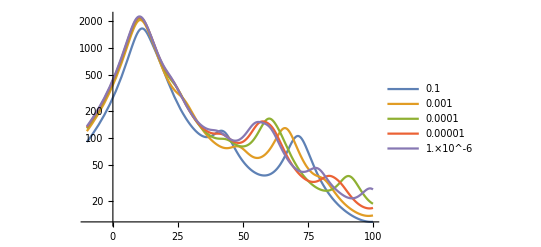

```mathematica
thresholds={0.1,0.001,0.0001,0.00001,0.000001};
LogPlot[Evaluate[((f=litcomp[#]/.σIm->σI)&/@thresholds)],{σRe,-10,100},PlotLegends->thresholds]
```

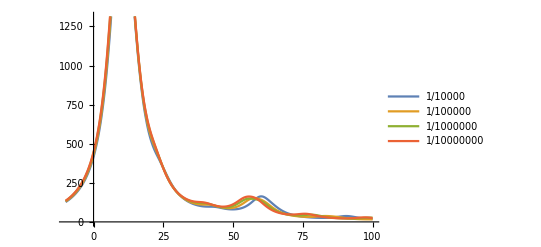

```mathematica
thresholds={10^-4,10^-5,10^-6,10^-7};
Plot[Evaluate[((f=litcomp[#]/.σIm->σI)&/@thresholds)],{σRe,-10,100},PlotLegends->thresholds]
```

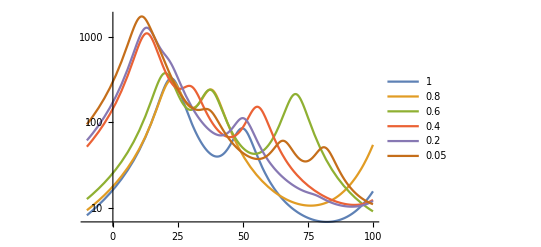

```mathematica
thresholds={1,0.8,0.6,0.4,0.2,0.05};
LogPlot[Evaluate[((f=litcomp[#]/.σIm->σI)&/@thresholds)],{σRe,-10,100},PlotRange->All,PlotLegends->thresholds]
```

```mathematica
Table[inhomo.PseudoInverse[norm,Tolerance->10^-n].inhomo,{n,10,0,-1}]
```

{69040.9,68369.1,67193.3,65468.7,64304.4,61086.2,57317.4,51177.5,25049.9,303.408,1.60484}

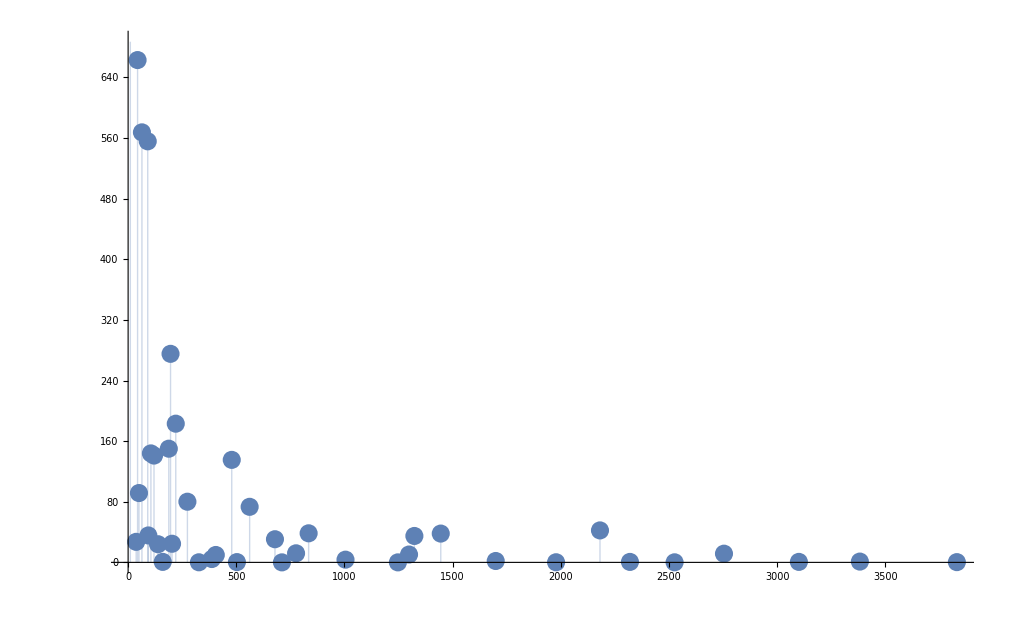

```mathematica
ListPlot[litshow[10^-4],Filling->Axis]
```